```mathematica
numberOfTrials = 0; 
probability = 1;
scorePerThrow = 0.5; 
results = List[];
iterator = 0; 
innerIter = 0; 
origBaseScore = 400; 
origBaseTarget = 395; 
target =origBaseTarget;
r=0;

While [iterator < 500, 
target = target + 0.01;   
runningProbability = 0; 
While [ innerIter < 10,
	(*Print["Ran Inner Iterator"];*)
	runningScore = origBaseScore;
	(*Print["Base Score is " + baseScore];*)
	ratio = target/origBaseScore; 
	While [ target>= runningScore -5∧ target ≤runningScore+5,
			(*Print[r++];*)
			If [ RandomInteger[1] == 0,
				runningScore = runningScore + scorePerThrow,
				runningScore  = runningScore - scorePerThrow
			   ];
			probability = probability * 0.5; 
		];
	(*Print[runningProbability + "running probability"];
	Print[probability + "momentProbability"];*)
	runningProbability = runningProbability + probability; 

	probability = 1; 
	innerIter++;
	];
(*Print[runningProbability + "Running Probability is" ];*)
innerIter = 0; 
totalProbability = runningProbability/10; 
(*Print[totalProbability];*)
runningProbability = 0; 
 
	(*Print["ONE HIT"]*)
	AppendTo[results, {runningScore,totalProbability}];

iterator++; 
]
results
```

{{400.5,0.325781},{400.5,0.225784},{400.5,0.287708},{400.5,0.312695},{390.,0.0820313},{400.5,0.303906},{400.5,0.16665},{400.5,0.228125},{400.5,0.237512},{400.5,0.300012},{400.5,0.176563},{400.5,0.20332},{400.5,0.33125},{400.5,0.225098},{400.5,0.240625},{400.5,0.1688},{400.5,0.365625},{390.,0.312598},{400.5,0.365625},{400.5,0.35},{400.5,0.325793},{400.5,0.350098},{400.5,0.275049},{400.5,0.278369},{400.5,0.325196},{400.5,0.28125},{400.5,0.215845},{390.,0.30625},{400.5,0.4125},{400.5,0.214893},{400.5,0.27832},{400.5,0.12511},{400.5,0.128223},{400.5,0.275781},{400.5,0.256445},{400.5,0.27832},{400.5,0.228137},{400.5,0.315625},{400.5,0.225052},{400.5,0.375},{400.5,0.350977},{400.5,0.3625},{400.5,0.213477},{400.5,0.3125},{400.5,0.2625},{400.5,0.213284},{400.5,0.203906},{400.5,0.154694},{400.5,0.27598},{401.,0.125},{401.,0.081374},{401.,0.118848},{401.,0.0332047},{401.,0.100391},{401.,0.0414124},{401.,0.0570443},{401.,0.0128908},{401.,0.0268127},{401.,0.156252},{401.,0.0954347},{390.5,0.0197327},{401.,0.100417},{401.,0.0891846},{401.,0.0265934},{401.,0.0770756},{390.5,0.0293213},{401.,0.102246},{401.,0.0765629},{401.,0.0255196},{390.5,0.0501221},{401.,0.0157242},{401.,0.071875},{401.,0.0578369},{401.,0.0359406},{401.,0.0187992},{401.,0.112506},{401.,0.0937561},{401.,0.100012},{401.,0.0863297},{390.5,0.0781509},{401.,0.059375},{390.5,0.0625977},{401.,0.0567444},{390.5,0.0384766},{401.,0.0754154},{401.,0.13291},{401.,0.0578125},{401.,0.0878967},{401.,0.0535156},{401.,0.112988},{401.,0.0704102},{401.,0.0629395},{401.,0.0399414},{401.,0.0644531},{401.,0.100031},{401.,0.103131},{401.,0.0691468},{390.5,0.0578186},{401.,0.0754276},{401.5,0.00161744},{401.5,0.00317693},{401.5,0.0267578},{401.5,0.0164673},{401.5,0.0158325},{401.5,0.0531374},{401.5,0.013331},{401.5,0.0187996},{401.5,0.0197762},{401.5,0.0166023},{401.5,0.013135},{401.5,0.0251465},{401.5,0.00317402},{401.5,0.0282257},{401.5,0.0132843},{401.5,0.0133339},{401.5,0.0289108},{401.5,0.0252472},{401.5,0.0330078},{401.5,0.0344238},{401.5,0.0195923},{401.5,0.021109},{401.5,0.015625},{401.5,0.0195801},{401.5,0.0162109},{401.5,0.0164185},{401.5,0.0384766},{401.5,0.00631409},{391.,0.0195313},{401.5,0.0314453},{401.5,0.0382935},{401.5,0.0348145},{401.5,0.01875},{401.5,0.0265755},{401.5,0.00722661},{401.5,0.0312502},{401.5,0.0219362},{401.5,0.021875},{401.5,0.00102615},{401.5,0.0289065},{401.5,0.0132936},{401.5,0.0421883},{401.5,0.0126984},{401.5,0.00722962},{401.5,0.0283722},{401.5,0.025},{401.5,0.012944},{401.5,0.0140625},{401.5,0.0375},{401.5,0.0164703},{402.,0.00197906},{402.,0.00625041},{402.,0.00161896},{402.,0.0203125},{402.,0.00169068},{402.,0.00012818},{391.5,0.00712891},{402.,0.00627632},{402.,0.0251222},{402.,0.0000247956},{402.,0.0141618},{402.,0.00161438},{402.,0.0015686},{391.5,0.000392532},{402.,0.00158696},{391.5,0.00673839},{391.5,0.00625},{402.,0.00316353},{402.,0.000422669},{402.,0.0141602},{402.,0.000226212},{402.,0.00673833},{402.,0.00207713},{402.,0.0140625},{402.,0.000103855},{402.,0.0144777},{402.,0.0128967},{402.,0.000488377},{402.,0.00361481},{402.,0.000104141},{402.,0.00666666},{402.,0.00373535},{391.5,5.96047×10^-8},{402.,0.000512695},{402.,0.000784326},{402.,6.10352×10^-6},{402.,0.000806069},{391.5,0.003162},{402.,0.00175946},{402.,0.00169067},{391.5,0.0203144},{402.,0.00169079},{391.5,0.00703125},{402.,0.00947266},{402.,0.00312815},{402.,0.000099279},{402.,0.000390626},{391.5,0.00166092},{402.,0.000610387},{402.,0.0125244},{402.5,0.0015686},{402.5,0.0000490196},{402.5,0.000928497},{402.5,0.00312595},{402.5,0.00390644},{392.,0.00390625},{402.5,5.0664×10^-8},{392.,7.62951×10^-7},{402.5,0.000785065},{402.5,0.00079422},{392.,0.0000488282},{402.5,2.32831×10^-10},{402.5,3.05176×10^-6},{402.5,0.00351887},{402.5,0.000293922},{392.,0.000794221},{402.5,5.89466×10^-11},{402.5,0.000199127},{392.,0.000842288},{392.,7.77852×10^-7},{402.5,0.00332108},{402.5,0.000293732},{392.,3.24251×10^-6},{402.5,0.00317383},{402.5,0.00312825},{392.,0.000784303},{392.,5.82077×10^-11},{402.5,0.00313721},{392.,3.05213×10^-6},{402.5,0.00469971},{402.5,0.003125},{402.5,0.00156251},{402.5,0.00020833},{402.5,0.00156345},{402.5,0.00312576},{402.5,0.00332055},{402.5,0.00312578},{402.5,0.000979805},{402.5,0.0000618013},{402.5,0.00255128},{402.5,0.0000488311},{402.5,0.00332108},{392.,0.00103779},{392.,0.0000488282},{402.5,0.000794232},{402.5,0.000793457},{392.,8.58307×10^-7},{402.5,0.0000518831},{402.5,0.000015259},{402.5,0.0000495911},{392.,0.00195332},{403.,0.000390631},{392.5,0.000396729},{403.,0.0000976563},{403.,0.00078125},{403.,6.10352×10^-6},{403.,0.0000488281},{403.,6.10389×10^-6},{392.5,6.19888×10^-6},{392.5,0.0000976622},{403.,0.00156879},{403.,0.00156298},{403.,0.0015626},{403.,0.0015625},{403.,0.000122073},{403.,0.000202942},{403.,4.7693×10^-7},{403.,0.0015625},{403.,0.000392158},{403.,1.52774×10^-6},{403.,0.00314951},{403.,9.03419×10^-9},{392.5,0.000592065},{403.,0.00312538},{403.,0.00156403},{403.,1.54978×10^-6},{403.,6.10352×10^-6},{403.,0.000123693},{403.,7.6294×10^-6},{403.,0.000104143},{403.,0.000415421},{403.,0.0000125946},{392.5,2.45884×10^-8},{403.,0.000123978},{403.,1.52588×10^-6},{392.5,5.96774×10^-9},{403.,0.000024426},{403.,1.91331×10^-6},{403.,9.68808×10^-8},{403.,0.000392151},{403.,1.90737×10^-6},{403.,0.00471194},{403.,0.0000245096},{403.,0.000415136},{403.,1.71673×10^-6},{403.,1.54972×10^-6},{403.,0.00039103},{403.,1.52625×10^-6},{392.5,1.91368×10^-6},{403.,7.7609×10^-6},{403.5,0.000012207},{403.5,4.76866×10^-8},{403.5,0.00021973},{403.5,0.0000518799},{403.5,3.05185×10^-6},{403.5,6.00267×10^-12},{403.5,1.90969×10^-7},{403.5,6.25851×10^-8},{403.5,0.000585988},{393.,0.000198376},{403.5,0.0000495911},{393.,0.000244141},{403.5,3.14731×10^-6},{403.5,2.04636×10^-13},{403.5,0.0000123985},{403.5,3.25441×10^-6},{403.5,7.62939×10^-7},{403.5,3.64598×10^-13},{393.,0.000781251},{403.5,0.000195313},{393.,1.1982×10^-8},{403.5,4.76837×10^-8},{393.,3.81488×10^-6},{393.,0.0000526907},{393.,0.0000488401},{403.5,7.63126×10^-7},{393.,3.72603×10^-9},{403.5,3.63798×10^-13},{393.,0.0000122072},{403.5,0.000390625},{403.5,1.86265×10^-10},{403.5,5.68479×10^-15},{393.,0.000195315},{403.5,0.000012207},{393.,0.0000488281},{403.5,4.77303×10^-8},{393.,1.90738×10^-7},{393.,0.000012207},{403.5,0.0000490785},{403.5,0.000012207},{393.,1.90736×10^-7},{403.5,0.0000124007},{403.5,0.0000488289},{403.5,1.71664×10^-6},{393.,3.33786×10^-7},{393.,0.000195313},{403.5,0.000244141},{393.,4.54748×10^-14},{403.5,8.1063×10^-7},{403.5,7.63172×10^-7},{404.,0.0000259459},{393.5,0.0000978533},{404.,6.10361×10^-6},{404.,1.01334×10^-7},{404.,6.10352×10^-6},{404.,4.76837×10^-7},{393.5,5.82079×10^-12},{404.,5.96192×10^-9},{404.,9.68575×10^-8},{404.,4.54579×10^-7},{393.5,6.71134×10^-9},{404.,0.0000244142},{404.,3.8445×10^-7},{404.,6.10361×10^-6},{393.5,7.62939×10^-7},{404.,6.10353×10^-6},{393.5,9.53908×10^-8},{404.,6.10354×10^-6},{393.5,1.52609×10^-6},{393.5,1.62125×10^-6},{404.,7.4506×10^-9},{404.,0.000392151},{404.,1.4916×10^-9},{404.,2.39394×10^-8},{404.,0.0000244394},{404.,9.31323×10^-11},{404.,0.0000976563},{393.5,3.78353×10^-10},{393.5,1.90782×10^-6},{393.5,1.51345×10^-9},{393.5,0.0000976566},{404.,2.98039×10^-8},{393.5,1.53482×10^-6},{404.,6.10948×10^-6},{393.5,0.0000244141},{404.,0.0000245579},{404.,1.49014×10^-9},{404.,0.00010376},{404.,7.62939×10^-6},{404.,1.90735×10^-7},{404.,2.78538×10^-13},{404.,5.68434×10^-15},{404.,0.0000125974},{404.,9.53674×10^-8},{393.5,1.52588×10^-6},{404.,9.53733×10^-8},{404.,5.55112×10^-18},{404.,1.5263×10^-6},{404.,3.90355×10^-19},{404.,7.86782×10^-7},{393.5,7.77841×10^-7},{394.,3.08828×10^-6},{394.,2.72865×10^-13},{394.,1.86266×10^-10},{404.5,1.91294×10^-7},{404.5,4.787×10^-8},{404.5,1.91131×10^-7},{394.,0.000012207},{404.5,9.61154×10^-8},{404.5,4.71848×10^-17},{394.,2.84219×10^-15},{404.5,9.65782×10^-7},{394.,7.62987×10^-7},{394.,2.45876×10^-8},{404.5,9.83477×10^-8},{394.,5.36675×10^-8},{404.5,3.63798×10^-13},{404.5,1.20141×10^-8},{394.,4.65803×10^-11},{404.5,1.49043×10^-9},{404.5,7.689×10^-7},{404.5,0.000195324},{404.5,1.23692×10^-11},{404.5,0.0000488281},{394.,2.02656×10^-7},{404.5,1.90747×10^-7},{404.5,7.7486×10^-7},{394.,3.8147×10^-7},{404.5,1.45608×10^-12},{404.5,2.98023×10^-9},{394.,3.57628×10^-8},{404.5,3.05213×10^-6},{404.5,0.000012207},{394.,2.71121×10^-21},{404.5,7.62975×10^-7},{404.5,3.72529×10^-10},{404.5,3.05772×10^-6},{404.5,1.52607×10^-6},{404.5,2.98102×10^-9},{404.5,1.8631×10^-10},{394.,3.72893×10^-10},{404.5,1.30443×10^-8},{404.5,1.9984×10^-16},{404.5,2.91038×10^-12},{394.,0.000012207},{404.5,2.40135×10^-11},{394.,1.62125×10^-6},{404.5,0.0000488283},{404.5,5.97793×10^-9},{404.5,3.05176×10^-6},{394.,1.16415×10^-11},{405.,5.82077×10^-12},{405.,1.62982×10^-9},{405.,1.49023×10^-9},{394.5,9.54606×10^-8},{405.,1.45524×10^-12},{394.5,2.98032×10^-9},{405.,1.98088×10^-10},{394.5,4.05312×10^-7},{394.5,4.65664×10^-11},{405.,3.02698×10^-9},{405.,2.468×10^-8},{405.,2.38419×10^-8},{405.,4.4412×10^-17},{394.5,8.73399×10^-12},{394.5,3.72529×10^-10},{394.5,4.76954×10^-8},{394.5,1.20141×10^-8},{394.5,2.91607×10^-12},{394.5,4.80577×10^-8},{405.,2.32834×10^-11},{405.,1.59874×10^-15},{405.,3.8147×10^-7},{405.,9.33142×10^-11},{405.,2.5332×10^-8},{394.5,7.39032×10^-13},{394.5,1.5259×10^-6},{394.5,8.8818×10^-17},{394.5,7.45172×10^-10},{394.5,4.80853×10^-8},{405.,6.7234×10^-6},{405.,5.82121×10^-12},{405.,4.80562×10^-8},{394.5,5.96337×10^-9},{394.5,2.91616×10^-12},{394.5,0.0000259399},{405.,1.23692×10^-11},{394.5,4.65889×10^-11},{394.5,3.05474×10^-6},{405.,4.91797×10^-8},{405.,4.36558×10^-12},{405.,4.66574×10^-11},{394.5,2.02662×10^-7},{394.5,1.59785×10^-9},{405.,1.36349×10^-16},{394.5,2.5338×10^-8},{405.,1.45519×10^-12},{405.,3.2756×10^-12},{394.5,2.0101×10^-10},{394.5,5.96092×10^-9},{394.5,3.55271×10^-16}}

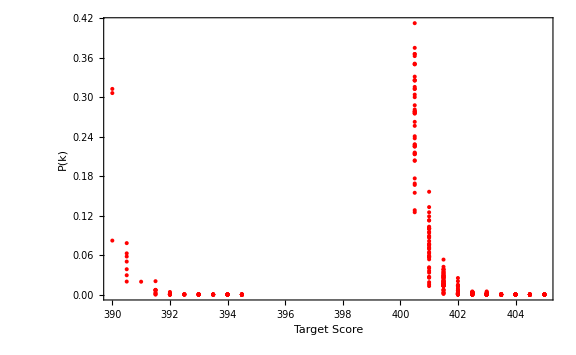

```mathematica
dataPlot = ListPlot[results,PlotRange->All,ImageSize->Large, Joined->False,Frame->True,FrameLabel->{"Target Score ","P(k)","",""}, LabelStyle->{FontSize->14, Directive[Bold,Black]},PlotStyle->{RGBColor[1,0,0],PointSize[0.005]}]
myFit = Fit[results,{0.4^x},x];
fitPlot = Plot[myFit,{x,400,404}];
Show[fitPlot,dataPlot];
```